```mathematica
Quit
```

XY 平面的 参数方程
-Graphics-

```mathematica
x0[X_,Y_]:=-1/2 Cos[2 π Y] (2+(-1+2 X) Sin[π Y])
y0[X_,Y_]:=-1/2 (2+(-1+2 X) Sin[π Y]) Sin[2 π Y]
z0[X_,Y_]:=-1/2 (-1+2 X) Cos[π Y]
```

```mathematica
{x0[X,Y],y0[X,Y],z0[X,Y]}/.{Y->1/2 Y}
```

{-1/2 Cos[π Y] (2+(-1+2 X) Sin[(π Y)/2]),-1/2 (2+(-1+2 X) Sin[(π Y)/2]) Sin[π Y],-1/2 (-1+2 X) Cos[(π Y)/2]}

```mathematica
ParametricPlot3D[%,{X,0,1},{Y,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
{x0[X_,Y_],y0[X_,Y_],z0[X_,Y_]}={-1/2 Cos[π Y] (2+(-1+2 X) Sin[(π Y)/2]),-1/2 (2+(-1+2 X) Sin[(π Y)/2]) Sin[π Y],-1/2 (-1+2 X) Cos[(π Y)/2]}
```

{-1/2 Cos[π Y] (2+(-1+2 X) Sin[(π Y)/2]),-1/2 (2+(-1+2 X) Sin[(π Y)/2]) Sin[π Y],-1/2 (-1+2 X) Cos[(π Y)/2]}

VX VY是主方向

```mathematica
VX=FullSimplify[{Derivative[1,0][x0][X,Y],Derivative[1,0][y0][X,Y],Derivative[1,0][z0][X,Y]}]
```

{-Cos[π Y] Sin[(π Y)/2],-Sin[(π Y)/2] Sin[π Y],-Cos[(π Y)/2]}

```mathematica
VY=FullSimplify[{Derivative[0,1][x0][X,Y],Derivative[0,1][y0][X,Y],Derivative[0,1][z0][X,Y]}]
```

{1/4 π Cos[(π Y)/2] (-2+4 X+(3-6 X) Cos[π Y]+8 Sin[(π Y)/2]),1/8 π (-8 Cos[π Y]+(-1+2 X) (Sin[(π Y)/2]-3 Sin[(3 π Y)/2])),1/4 π (-1+2 X) Sin[(π Y)/2]}

一些不变量

```mathematica
E0[X_,Y_]=FullSimplify[VX.VX]
```

1

```mathematica
G0[X_,Y_]=FullSimplify[VY.VY]
```

1/16 π^2 (19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])

面上任一点的两个切向量正交

```mathematica
F0[X_,Y_]=FullSimplify[VX.VY]
```

0

VN 是面的法向

```mathematica
VN=FullSimplify[Cross[VX,VY]]
```

{-1/4 π Cos[(π Y)/2] (4 Cos[π Y]+(-1+2 X) (Sin[(π Y)/2]+Sin[(3 π Y)/2])),1/4 π ((-1+2 X) Cos[π Y]+(1-2 X-2 Csc[(π Y)/2]) Sin[π Y]^2),1/2 π Sin[(π Y)/2] (2+(-1+2 X) Sin[(π Y)/2])}

单位化

```mathematica
NVN=FullSimplify[VN/(Sqrt[VN.VN])]
```

{-(Cos[(π Y)/2] (4 Cos[π Y]+(-1+2 X) (Sin[(π Y)/2]+Sin[(3 π Y)/2])))/(√(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])),((-1+2 X) Cos[π Y]+(1-2 X-2 Csc[(π Y)/2]) Sin[π Y]^2)/(√(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])),(2 Sin[(π Y)/2] (2+(-1+2 X) Sin[(π Y)/2]))/(√(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2]))}

主方向的二阶导

```mathematica
VXX=FullSimplify[{Derivative[2,0][x0][X,Y],Derivative[2,0][y0][X,Y],Derivative[2,0][z0][X,Y]}]
```

{0,0,0}

```mathematica
VXY=FullSimplify[{Derivative[1,1][x0][X,Y],Derivative[1,1][y0][X,Y],Derivative[1,1][z0][X,Y]}]
```

{1/4 π (Cos[(π Y)/2]-3 Cos[(3 π Y)/2]),1/4 π (Sin[(π Y)/2]-3 Sin[(3 π Y)/2]),1/2 π Sin[(π Y)/2]}

```mathematica
VYY=FullSimplify[{Derivative[0,2][x0][X,Y],Derivative[0,2][y0][X,Y],Derivative[0,2][z0][X,Y]}]
```

{1/16 π^2 (16 Cos[π Y]+(-1+2 X) (-Sin[(π Y)/2]+9 Sin[(3 π Y)/2])),1/8 π^2 Cos[(π Y)/2] (-5+10 X+(9-18 X) Cos[π Y]+16 Sin[(π Y)/2]),1/8 π^2 (-1+2 X) Cos[(π Y)/2]}

一些不变量

```mathematica
L0[X_,Y_]=FullSimplify[VXX.NVN]
```

0

```mathematica
N0[X_,Y_]=FullSimplify[VYY.NVN]
```

(π^2 Cos[(π Y)/2] (-10-8 (-1+X) X+(1-2 X)^2 Cos[π Y]+(8-16 X) Sin[(π Y)/2]))/(2 √(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2]))

```mathematica
M0[X_,Y_]=FullSimplify[VXY.NVN]
```

(2 π)/(√(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2]))

计算生长函数
-Graphics-

```mathematica
Assum1=X>0&&Y>0;
```

```mathematica
λ10=Simplify[√E0[X,Y],Assum1]
λ20=Simplify[√G0[X,Y],Assum1]
```

1

1/4 π √(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])

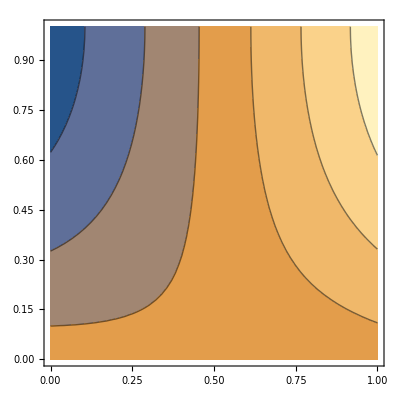

```mathematica
ContourPlot[λ20,{X,0,1},{Y,0,1}]
```

```mathematica
λ11=Simplify[(-L0[X,Y]λ10)/E0[X,Y],Assum1]
```

0

```mathematica
λ12=Simplify[(-N0[X,Y]λ20)/G0[X,Y],Assum1]
```

-(2 π Cos[(π Y)/2] (-10-8 (-1+X) X+(1-2 X)^2 Cos[π Y]+(8-16 X) Sin[(π Y)/2]))/(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])

```mathematica
λs=Simplify[(-2M0[X,Y]λ10 λ20)/(G0[X,Y] λ10+E0[X,Y] λ20),Assum1]
```

-((16 π)/(4 √(19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])+π (19+12 (-1+X) X-2 (1-2 X)^2 Cos[π Y]+16 (-1+2 X) Sin[(π Y)/2])))

可以观察一下参考构型与当前构型各点间的对应关系

```mathematica
P1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,1},{Y,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
{UMin,UMax}={0,1};
{VMin,VMax}={0,1};
```

```mathematica
a=2;
```

```mathematica
ParametricPlot3D[{x0[U,V],y0[U,V],z0[U,V]}, {U,UMin,UMax},{V,VMin,UMax},PlotRange->All,PlotStyle->LightBlue];
ParametricPlot3D[{U,V,0},{U,UMin,UMax},{V,VMin,UMax},PlotRange->All,PlotStyle->Green];
RefCur=Show[%%,%];
```

```mathematica
Manipulate[Show[RefCur,ListPointPlot3D[Evaluate[{{x0[U,V],y0[U,V],z0[U,V]},{U,V,0}}/.{U-> a,V-> b}],PlotStyle->PointSize[Large]]],{a,UMin,UMax},{b,UMin,UMax}]
```